# Playing with precomputed g values

In the other file, we compute g values and append them to the file “computedG.csv”. In this file, we import the data from this file just to look at it. Recall that for the computation, we store polynomials as arrays; that is, a+bk+ck^3 == {a,b,0,c}. For viewing purposes, in this file, we convert them back to polynomials in k.

```mathematica
Remove["Global`*"];
```

```mathematica
gFilename="/Users/jtiosue/Documents/Repositories/LXEB/Julia/computedG.csv";
```

```mathematica
g=Association@@Table[
{tup[[1]],tup[[{2,3,4}]]}->∑_(i=0)^(Length[tup]-5) tup[[5+i]] k^i,
{tup,Import@gFilename}
];
```

### How many have we computed so far?

```mathematica
g//Length
```

239

### Print all of the a={0,0,0} entries

```mathematica
ns=Select[Keys@g,#[[2]]=={0,0,0}&][[All,1]]//Sort;
```

```mathematica
Table[
{n,g[{n,{0,0,0}}]},
{n,ns}
]//TableForm
```

1 | 2 k+2 k^2
2 | 176 k+184 k^2+64 k^3+8 k^4
3 | 74880 k+90336 k^2+40752 k^3+8976 k^4+1008 k^5+48 k^6
4 | 90408960 k+121065984 k^2+63951360 k^3+17759616 k^4+2872320 k^5+278016 k^6+15360 k^7+384 k^8
5 | 237617971200 k+343673303040 k^2+202717824000 k^3+65407180800 k^4+12943123200 k^5+1655781120 k^6+139392000 k^7+7603200 k^8+249600 k^9+3840 k^10
6 | 1159859699712000 k+1780791422976000 k^2+1140813555425280 k^3+410191172628480 k^4+93270554265600 k^5+14247651916800 k^6+1508640215040 k^7+112075453440 k^8+5807462400 k^9+203443200 k^10+4423680 k^11+46080 k^12
7 | 9462639862480896000 k+15246273259929600000 k^2+10421808429874544640 k^3+4071608172016680960 k^4+1026952754189967360 k^5+178307659157483520 k^6+22109565749483520 k^7+1998175940167680 k^8+132745496647680 k^9+6466813839360 k^10+227377059840 k^11+5549967360 k^12+85800960 k^13+645120 k^14
8 | 119720630833266032640000 k+200796561000272756736000 k^2+144711123926956218777600 k^3+60415241009583386787840 k^4+16528349328270038138880 k^5+3166169317852953968640 k^6+441843922442755768320 k^7+46026366788113367040 k^8+3629790873271664640 k^9+218065033148497920 k^10+9969100754780160 k^11+343607014195200 k^12+8742088212480 k^13+157223485440 k^14+1816657920 k^15+10321920 k^16
9 | 2221247018056830041456640000 k+3855175197947055480766464000 k^2+2904237338727171996883353600 k^3+1280729580277534827070095360 k^4+374303224008993996354355200 k^5+77564194739580892836003840 k^6+11877470107076545413120000 k^7+1380287720700295139819520 k^8+123832881173454682521600 k^9+8665188337608815738880 k^10+475146042332361523200 k^11+20406933381977210880 k^12+682378385994547200 k^13+17534066558238720 k^14+337908282163200 k^15+4664186634240 k^16+41803776000 k^17+185794560 k^18

## Run our various tests on the values

### Check n=3, a = {0,0,0}

```mathematica
g[{3,{0,0,0}}]==74880 k+90336 k^2+40752 k^3+8976 k^4+1008 k^5+48 k^6
```

True

### Check that the sum of the coefficients is equal to the number of graphs

```mathematica
graphCounter[n_,a_]:=With[{a12=a[[1]],a13=a[[2]],a23=a[[3]]},
Binomial[2 n,a12] Binomial[2 n-a12,a13]*Binomial[2 n,a12] Binomial[2 n-a12,a23]*Binomial[2 n,a13] Binomial[2 n-a13,a23]*a12!*a13!*a23!*(2 n-a12-a13-1)!!*(2 n-a12-a23-1)!!*(2 n-a13-a23-1)!!*4^n
];
```

```mathematica
Table[
(g[key]/.k->1)==graphCounter@@key,
{key,Keys@g}
]//AllTrue[#&]
```

True

### Check the coefficient of the highest degree

```mathematica
(*coef[n_]:=(2n-1)!!+∑_(i=1)^n (2i-1)!!(2n-2i-1)!!Binomial[n,i];*)
coef[n_]=(2n)!!;
```

```mathematica
Table[
CoefficientList[g[{n,{0,0,0}}],k][[-1]]==coef@n,
{n,ns}
]//AllTrue[#&]
```

True

### Check that the number of a for a given n is less than roughly n^3

```mathematica
counting=ConstantArray[0,Length@ns];
Do[
counting[[key[[1]]]]+=1;,
{key,Keys@g}
];
```

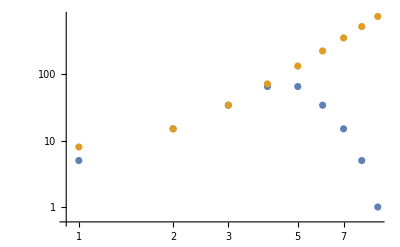

```mathematica
ListLogLogPlot@{counting,ns^3+7}
```

```mathematica
hafnian[n_]:=(2n-1)!!g[{n,{0,0,0}}];
```

## Plot coefficients of k

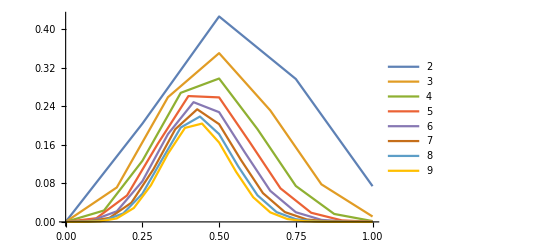

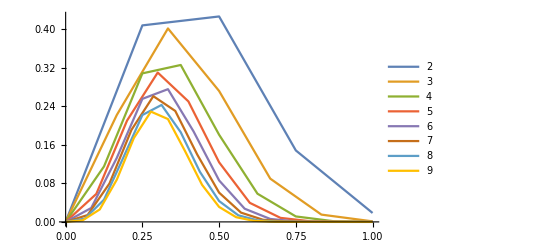

```mathematica
l[n_]:=CoefficientList[g[{n,{0,0,0}}],k];
t[n_,kk_]:=With[{ll=l@n,tot=g[{n,{0,0,0}}]/.k->kk@n},
Table[{(i-1)/(Length@ll-1),ll[[i]](kk@n)^(i-1)/tot},{i,Length@ll}]
];
plot[nns_,kk_]:=ListPlot[Table[t[n,kk],{n,nns}],PlotLegends->nns,Joined->True,PlotRange->All];
plot[Drop[ns,1],#&] (* k = n *)
plot[Drop[ns,1],#/2&] (* k = n/2 *)
```